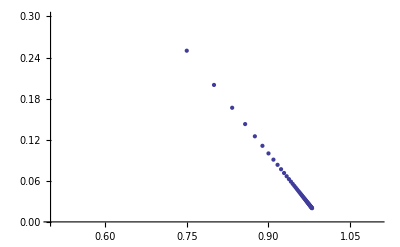

```mathematica
x[n_]:={(n-1)/n,1/n}
ListPlot[Table[x[n],{n,1,50}],PlotRange->{{0.5,1.1},{0,0.3}}]
```

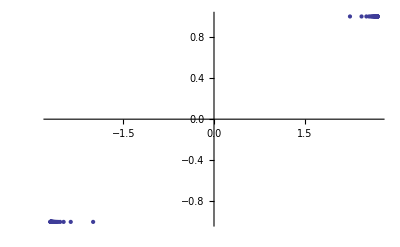

```mathematica
x[n_]:={(-(n+1)/n)^n,(-1)^n}
ListPlot[Table[x[n],{n,1,100}]]
```

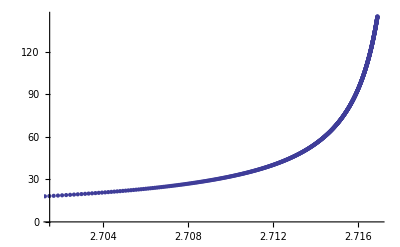

```mathematica
x[n_]:={(1+1/n)^n,n/Log[1+n]}
ListPlot[Table[x[n],{n,1,1000}]]
```

```mathematica
x[n_]:={Sin[n*Pi/2],Cos[n*Pi/2],n/10}
Graphics3D[Point[Table[x[n],{n,1,100}]]]
```

-Graphics3D-